## Agenda

Haddamard walk. Moneda fija, qué estado inicial produce Parrondo?

## Definiciones

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../../libs/QuantumWalks.wl"]
```

```mathematica
Get["../../libs/QMB.wl"]
```

```mathematica
?QMB`*
```

```mathematica
(*moneda*)
ClearAll[c]
c[θ_,α_,ϕ_]:=FullSimplify[MatrixExp[-I*θ/2.*({Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}.(PauliMatrix/@{1,2,3}))]]
```

```mathematica
H=Chop[Exp[I*Pi/2]Chop[c[Pi,Pi/4.,0.]]]
```

{{0.707107,0.707107},{0.707107,-0.707107}}

```mathematica
(*shift*)
ClearAll[S]
S[t_]:=KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],1],{{0,0},{0,1.}}]+KroneckerProduct[DiagonalMatrix[ConstantArray[1,2t],-1],{{1.,0},{0,0}}]
```

```mathematica
(*paso DTQW*)
ClearAll[U]
U[t_,θ_,α_,ϕ_]:=S[t].KroneckerProduct[IdentityMatrix[2t+1],c[θ,α,ϕ]]
```

```mathematica
(*DTQWAnalytical*)
ClearAll[DTQWAnalytical]
DTQWAnalytical[t_,θ_,α_,ϕ_]:=Fold[ArrayPad[U[#2,θ,α,ϕ].#1,2]&,{0,0,0,1,0,0},Range[t]]
DTQWAnalytical[psi0_,t_,theta_,alpha_,phi_]:=Module[{validInput},validInput=MatchQ[psi0,{_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ,_?NumericQ}];
If[!validInput,Message[DTQWAnalytical::invalidpsi0,psi0];
Return[$Failed];];
Fold[ArrayPad[U[#2,theta,alpha,phi].#1,2]&,psi0,Range[t]]]

DTQWAnalytical::invalidpsi0="ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: `1`.";
```

```mathematica
(*probabilidades espacio*)
ProbDistPosition[ψ_]:=Total/@(Abs[Partition[ψ,2]]^2)
```

```mathematica
(*expected position*)
ClearAll[ExpPosition]
ExpPosition[t_,θ_,α_,ϕ_]:=ProbDistPosition[DTQWAnalytical[t,θ,α,ϕ]].Range[-t-1,t+1]
ExpPosition[ψ_]:=Module[{t=(Length[ψ]/2-3)/2},Chop[ProbDistPosition[ψ].Range[-t-1,t+1]]]
```

```mathematica
PlotSphere[angles1_,angles2_,ψ_]:=
Module[{theta1,phi1,x1,y1,z1,vector1,theta2,phi2,x2,y2,z2,vector2,theta3,phi3,x3,y3,z3,vector3,axes,sphere},
{theta1,phi1}=angles1;
{theta2,phi2}=angles2;
{theta3,phi3}={2ArcCos[Abs[#1]],Arg[#2]-Arg[#1]}&@@(ψ);

{x1,y1,z1}={Sin[theta1] Cos[phi1],Sin[theta1] Sin[phi1],Cos[theta1]};
vector1={Thick,Black,Arrow[{{0,0,0},{x1,y1,z1}}]};

{x2,y2,z2}={Sin[theta2] Cos[phi2],Sin[theta2] Sin[phi2],Cos[theta2]};
vector2={Thick,Black,Arrow[{{0,0,0},{x2,y2,z2}}]};

{x3,y3,z3}={Sin[theta3] Cos[phi3],Sin[theta3] Sin[phi3],Cos[theta3]};
vector3={Thick,Orange,Arrow[{{0,0,0},{x3,y3,z3}}]};

axes={{Red,Arrow[{{0,0,0},{1.2,0,0}}]},{Green,Arrow[{{0,0,0},{0,1.2,0}}]},{Thick,Blue,Arrow[{{0,0,0},{0,0,1.2}}]}};
sphere=ParametricPlot3D[{Sin[u] Cos[v],Sin[u] Sin[v],Cos[u]},{u,0,Pi},{v,0,2 Pi},Mesh->{7,7},MeshStyle->Directive[Opacity[0.1],Gray],PlotStyle->Opacity[0.15],Lighting->"Neutral",Boxed->False,Axes->False,ImageSize->400,ImagePadding->None,ImageMargins->0,PlotRange->All
];

Show[{sphere,Graphics3D[{vector1,vector2,vector3,axes}]},PlotRange->All,ViewPoint->{2,2,2}]
]
```

```mathematica
Options[PlotExpValPosition]={FontSize->28,MaxTime->50,ImageSize->600,PlotLegendsPosition->{Left,Top}};

PlotExpValPosition[ψ0_,angles1_,angles2_,OptionsPattern[]]:=
Module[{α1,α2,θ1,θ2,ϕ1,ϕ2,c1,c2},
{θ1,α1,ϕ1}=angles1;
{θ2,α2,ϕ2}=angles2;

(*monedas*)
c1=c[θ1,α1,ϕ1];
c2=c[θ2,α2,ϕ2];

ListPlot[Prepend[Table[{t,Chop[ExpValPosition[DTQW[ψ0,t,#],t]]},{t,OptionValue[MaxTime]}],{0,0}]&/@{c1,c2,c1.c2},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]], "⟨x⟩"},
FrameStyle->Directive[Black,OptionValue[FontSize]],
ImageSize->OptionValue[ImageSize],
PlotLegends->
Placed[
{"C_1("<>ToString[NumberForm[θ1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[α1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ1/Pi,{Infinity,2}]]<>"π)","C_2("<>ToString[NumberForm[N[θ2/Pi],{Infinity,2}]]<>"π, "<>ToString[NumberForm[α2/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ2/Pi,{Infinity,2}]]<>"π)","C_1C_2"},
OptionValue[PlotLegendsPosition]
],
PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[ψ0[[1]],{Infinity,3}]]<>"|0⟩+("<>ToString[NumberForm[ψ0[[2]],{Infinity,3}]]<>")|1⟩",Black,OptionValue[FontSize]],
LabelStyle->Directive[Black,OptionValue[FontSize]]
]
]
```

```mathematica
PlotSphere[angles1_,angles2_,ψ_,c_]:=
Module[{theta1,phi1,x1,y1,z1,vector1,theta2,phi2,x2,y2,z2,vector2,theta3,phi3,x3,y3,z3,vector3,theta4,phi4,x4,y4,z4,vector4,axes,sphere},
{theta1,phi1}=angles1;
{theta2,phi2}=angles2;
{theta3,phi3}={2ArcCos[Abs[#1]],Arg[#2]-Arg[#1]}&@@(ψ);

{x1,y1,z1}={Sin[theta1] Cos[phi1],Sin[theta1] Sin[phi1],Cos[theta1]};
vector1={Thick,Black,Arrow[{{0,0,0},{x1,y1,z1}}]};

{x2,y2,z2}={Sin[theta2] Cos[phi2],Sin[theta2] Sin[phi2],Cos[theta2]};
vector2={Thick,Black,Arrow[{{0,0,0},{x2,y2,z2}}]};

{x3,y3,z3}={Sin[theta3] Cos[phi3],Sin[theta3] Sin[phi3],Cos[theta3]};
vector3={Thick,Orange,Arrow[{{0,0,0},{x3,y3,z3}}]};

{theta4,phi4}=RotationAxisAndAngle[c][[2;;]];
{x4,y4,z4}={Sin[theta4] Cos[phi4],Sin[theta4] Sin[phi4],Cos[theta4]};
vector4={Thick,Purple,Arrow[{{0,0,0},{x4,y4,z4}}]};

(*Generar trayectorias rotadas para varios ángulos*)
angles=Subdivide[0,2 Pi,100];
rotatedVectors=Table[RotationTransform[angle,{x4,y4,z4}][{x3,y3,z3}],{angle,angles}];

axes={{Red,Arrow[{{0,0,0},{1.2,0,0}}]},{Green,Arrow[{{0,0,0},{0,1.2,0}}]},{Thick,Blue,Arrow[{{0,0,0},{0,0,1.2}}]}};
sphere=ParametricPlot3D[{Sin[u] Cos[v],Sin[u] Sin[v],Cos[u]},{u,0,Pi},{v,0,2 Pi},Mesh->{7,7},MeshStyle->Directive[Opacity[0.1],Gray],PlotStyle->Opacity[0.15],Lighting->"Neutral",Boxed->False,Axes->False,ImageSize->400,ImagePadding->None,ImageMargins->0,PlotRange->All
];

Show[{sphere,Graphics3D[{vector1,vector2,vector3,vector4,axes,{Blue,Line[rotatedVectors]}}]},PlotRange->All,ViewPoint->{2,2,2}]
]
```

```mathematica
(*Función para extraer ángulo de rotación y eje en coordenadas esféricas*)RotationAxisAndAngle[U_]:=Module[{a,bvec,theta,n,thetaPolar,phiAzimuthal,sigmaX,sigmaY,sigmaZ},
(*Definir matrices de Pauli*)sigmaX={{0,1},{1,0}};
sigmaY={{0,-I},{I,0}};
sigmaZ={{1,0},{0,-1}};
(*Parte escalar*)a=Re[Tr[U]]/2;
(*Parte vectorial*)bvec=Im[{Tr[U.sigmaX],Tr[U.sigmaY],Tr[U.sigmaZ]}]/2;
(*Ángulo de rotación*)theta=2 ArcCos[a];
(*Eje normalizado*)n=Normalize[bvec];
(*Coordenadas esféricas del eje*)
{theta,ArcCos[n[[3]]],ArcTan[n[[1]],n[[2]]]}]
(*<|"RotationAngle"->theta,"RotationAxis"->n,"PolarAngleTheta"->thetaPolar,"AzimuthalAnglePhi"->phiAzimuthal|>]*)

(*Ejemplo:rotación pi/2 alrededor del eje (1,1,1)/Sqrt[3]*)
nExample=Normalize[{1,1,1}];
thetaExample=Pi/2;
UExample=MatrixExp[-I thetaExample/2 (nExample.{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]})];

(*Resultado*)
RotationAxisAndAngle[UExample]
```

{π/2,ArcCos[-1/(√3)],-(3 π)/4}

## Cálculos

```mathematica
t=5;a=0.;b=1.;
Manipulate[
Plot[Evaluate[ExpPosition[#,θ,α,ϕ]&/@Range[t]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,1}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,1}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;a=1.;b=0.;
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,1}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,1}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

```mathematica
t=5;
Module[{ψ0},
ψ0={1,1}/√2.;
Manipulate[
{Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[ψ0,2],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[ψ0[[1]],{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[ψ0[[2]],{Infinity,3}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->22],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
],
PlotExpValPosition[ψ0,{θ1,α,ϕ},{θ2,α,ϕ},FontSize->22]
}
,{α,0,Pi},{ϕ,0,2Pi},
{θ1,0,2Pi},{θ2,0,2Pi}]
]
```

```mathematica
ClearAll[tmax]
```

```mathematica
Manipulate[
Module[{θ1,α1,ϕ1,θ2,α2,ϕ2,ψ0},
ψ0={1,1}/√2.;
{θ1,α1,ϕ1}={1.74Pi,0.18Pi,1.74Pi};
{θ2,α2,ϕ2}={(1.57+x)Pi,(0.18+y)Pi,(1.74+z)Pi};
u=c[θ1,α1,ϕ1].c[θ2,α2,ϕ2];
{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},tmax->50,FontSize->24],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0,u]}
]
,{x,0,2,0.1},{y,0,1,0.1},{z,0,2,0.1}]
```

```mathematica
θ=Pi/.4;MatrixExp[-I*θ/2*Pauli[3]]
```

SparseArray[…]

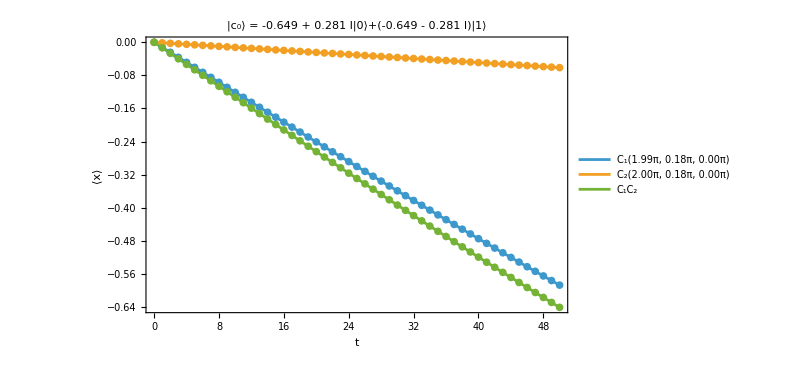
{-Graphics-,-Graphics3D-}

```mathematica
x=-1.74Pi+0.Pi;ClearAll[tmax];
ψ0=MatrixExp[-I*x/2*Pauli[3]].{1,1}/√2.;
{θ1,α1,ϕ1}={(1.74+0.25)Pi,0.18Pi,1.74Pi+x};
{θ2,α2,ϕ2}={1.999Pi,(0.18+0)Pi,1.74Pi+x};
u=c[θ1,α1,ϕ1].c[θ2,α2,ϕ2];
{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},tmax->50,FontSize->24],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0,u]}
```

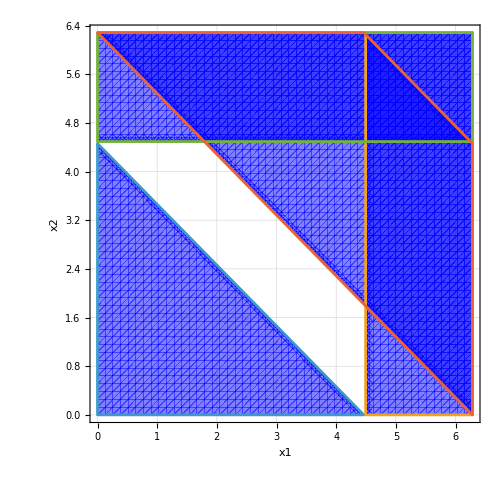

```mathematica
RegionPlot[{0<x1+x2<=1.42*Pi,1.43*Pi<=x1<2*Pi,1.43*Pi<=x2<2*Pi,2Pi<x1+x2<=2Pi+1.42*Pi},{x1,0,2*Pi},{x2,0,2*Pi},PlotPoints->50,FrameLabel->{"x1","x2"},GridLines->Automatic,PlotStyle->Directive[Opacity[0.5],Blue],ImageSize->500]
```

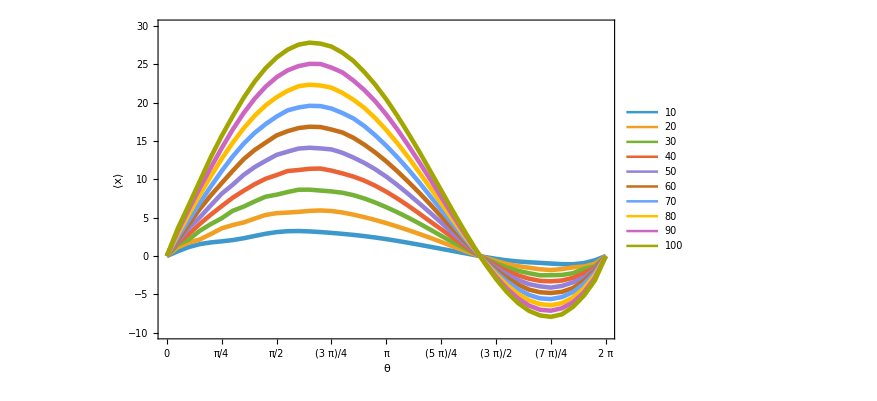

```mathematica
{tmin,tmax,dt}={10,100,10};
ψ0=MatrixExp[-I*(-1.74Pi)/2*Pauli[3]].{1,1}/√2.;
α=0.18Pi;
fig=ListPlot[Table[{#,ExpValPosition[DTQW[ψ0,t,c[#,α,0]],t]}&/@Range[0,2Pi,0.05Pi],{t,tmin,tmax,dt}],
PlotRange->{Automatic,{-10,30}},
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->22],
ImageSize->650,
(*PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[ψ0[[1]],{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[ψ0[[2]],{Infinity,3}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[0./Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->22],*)
PlotLegends->Range[tmin,tmax,dt],
LabelStyle->Directive[Black,FontSize->22],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
```

```mathematica
filename="../parrondo/figs/fixed_rotation_axes_expval_01.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
RunProcess[{"pdfcrop",filename,filename}]
```

../parrondo/figs/fixed_rotation_axes_expval_01.pdf

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `../parrondo/figs/fixed_rotation_axes_expval_01.pdf'.
,StandardError→|>

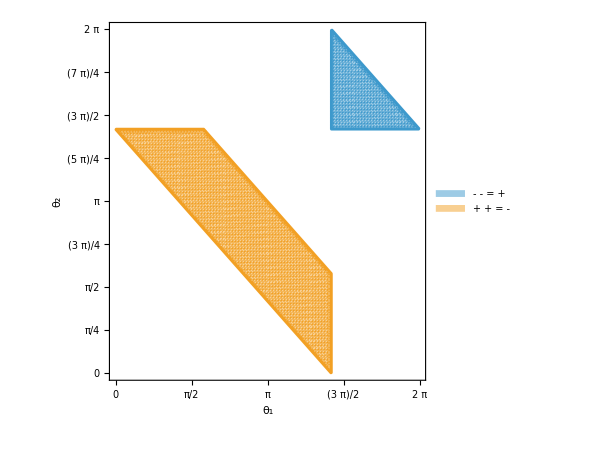

```mathematica
fig=RegionPlot[{1.42*Pi<=x1<=2*Pi&&1.42*Pi<=x2<=2*Pi&&2Pi<=x1+x2<=2Pi+1.42*Pi,(*x1<=2Pi&&x2<=4Pi&&x1+x2>=2Pi+1.42*Pi,2Pi<=x1+x2<=2Pi+1.42*Pi,*)2.Pi>=x1+x2>=0.+1.42*Pi&&x2<=1.42Pi&&x1<=1.42Pi},{x1,0,2*Pi},{x2,0,2*Pi},PlotPoints->100,FrameLabel->{"θ_1","θ_2"},
PlotLegends->Placed[
SwatchLegend[
{"- - = +","+ + = -"},
LegendMarkerSize->30
],
{Left,Top}
],
LabelStyle->Directive[Black,FontSize->22],
GridLines->Automatic,
PlotStyle->Directive[Opacity[0.5]],
FrameTicks->{{Table[{k Pi/4,TraditionalForm[k Pi/4]},{k,0,8}],Automatic},{Table[{k Pi/4,TraditionalForm[k Pi/4]},{k,0,8}],Automatic}},
FrameStyle->Directive[Black,FontSize->22],
ImageSize->450
]
```

```mathematica
filename="../parrondo/figs/fixed_rotation_axes_01.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
RunProcess[{"pdfcrop",filename,filename}]
```

../parrondo/figs/fixed_rotation_axes_01.pdf

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `../parrondo/figs/fixed_rotation_axes_01.pdf'.
,StandardError→|>

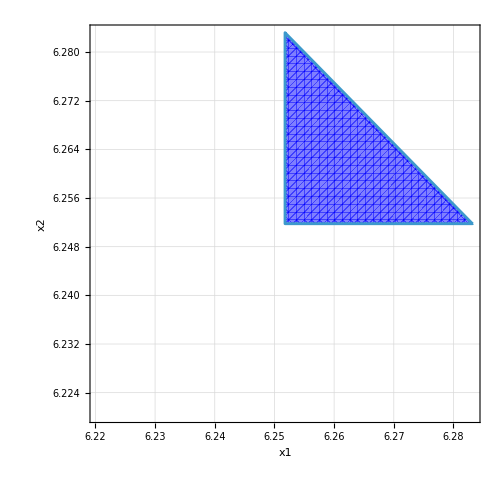

```mathematica
RegionPlot[{(*0<x1+x2<=1.99Pi,*)1.99Pi<=x1<2*Pi&&1.99*Pi<=x2<2*Pi&&2Pi<x1+x2<=2Pi+1.99*Pi},{x1,1.98Pi,2*Pi},{x2,1.98Pi,2*Pi},PlotPoints->50,FrameLabel->{"x1","x2"},GridLines->Automatic,PlotStyle->Directive[Opacity[0.5],Blue],ImageSize->500]
```

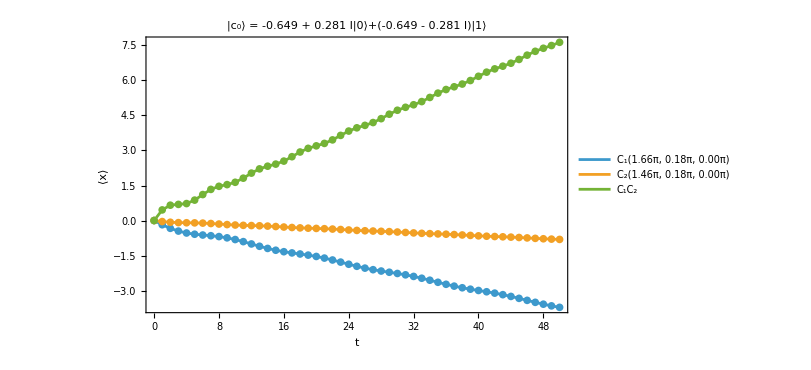
{-Graphics-,-Graphics3D-}

```mathematica
x=-1.74Pi;
ψ0=MatrixExp[-I*x/2*Pauli[3]].{1,1}/√2.;
{θ1,α1,ϕ1}={5.2,0.18Pi,1.74Pi+x};
{θ2,α2,ϕ2}={4.6,(0.18+0)Pi,1.74Pi+x};
u=c[θ1,α1,ϕ1].c[θ2,α2,ϕ2];
{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},tmax->50,FontSize->24],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0,u]}
```

## Variando α

```mathematica
t=5;
x=-1.74Pi+0.Pi;
ψ0=MatrixExp[-I*x/2*Pauli[3]].{1,1}/√2.;
Manipulate[
{Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[ψ0,2],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[ψ0[[1]],{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[ψ0[[2]],{Infinity,3}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->22],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
],
PlotExpValPosition[ψ0,{θ1,α,ϕ},{θ2,α,ϕ},FontSize->22]
}
,{α,0.9Pi,Pi,0.01Pi},{ϕ,0,2Pi},
{θ1,0,2Pi},{θ2,0,2Pi}]
```

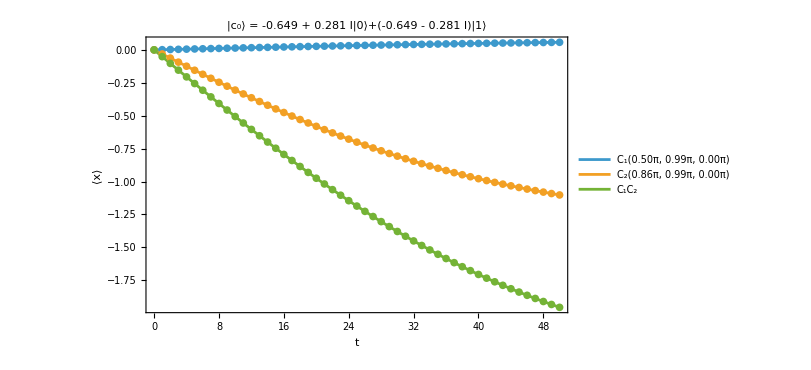
{-Graphics-,-Graphics3D-}

```mathematica
x=-1.74Pi+0.Pi;
ψ0=MatrixExp[-I*x/2*Pauli[3]].{1,1}/√2.;
α1=α2=0.99Pi;
{θ1,ϕ1}={0.5Pi,1.74Pi+x};
{θ2,ϕ2}={2.7,1.74Pi+x};
u=c[θ1,α1,ϕ1].c[θ2,α2,ϕ2];
{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},tmax->50,FontSize->24],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0,u]}
```

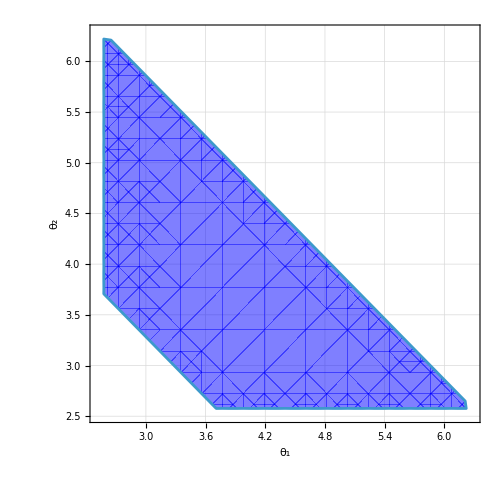

```mathematica
RegionPlot[{0.82Pi<=x1<2*Pi&&0.82*Pi<=x2<2*Pi&&2Pi<x1+x2<=2Pi+0.82*Pi},{x1,0.8Pi,2*Pi},{x2,0.8Pi,2*Pi},PlotPoints->10,FrameLabel->{"θ_1","θ_2"},FrameStyle->Directive[Black,FontSize->26],GridLines->Automatic,PlotStyle->Directive[Opacity[0.5],Blue],ImageSize->500]
```

```mathematica
Mod[1.99+1.44,2]
```

1.43

```mathematica
nhat[θ_,ϕ_]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
```

```mathematica
nhat[α1,ϕ1].{1,0,0}
```

0.366799

```mathematica
y=0.02;nhat[α1+y,ϕ1+z].nhat[Pi/2.+y,0+z]
```

0.361541

```mathematica
Cross[nhat[α1,ϕ1],{1,0,0}]
```

{0.,0.844328,0.390601}

```mathematica
RotationMatrix[Pi/2,{0,0,1}].{1,0,0}
```

{0,1,0}

```mathematica
RotationMatrix[Pi/2,Cross[nhat[α1,ϕ1],{1,0,0}]].nhat[α1,ϕ1]
RotationMatrix[Pi/2,Cross[nhat[α1,ϕ1],{1,0,0}]].{1,0,0}
```

{0.9303,0.154006,-0.332901}

{0.,0.419865,-0.907586}

```mathematica
{0.9303003423857524,0.15400607441608416,-0.3329014899334328}.{0.,0.4198653977378515,-0.9075863858511959}
```

0.366799

```mathematica
ArcCos[1-0.3329014899334328]
```

0.840489

```mathematica
ArcTan[0.15400607441608416/0.9303003423857524]
```

0.164057

```mathematica
nhat[α1,ϕ1].
```

```mathematica
ArcCos[nhat[α1,ϕ1].{1,0,0}]/Pi
```

0.380454

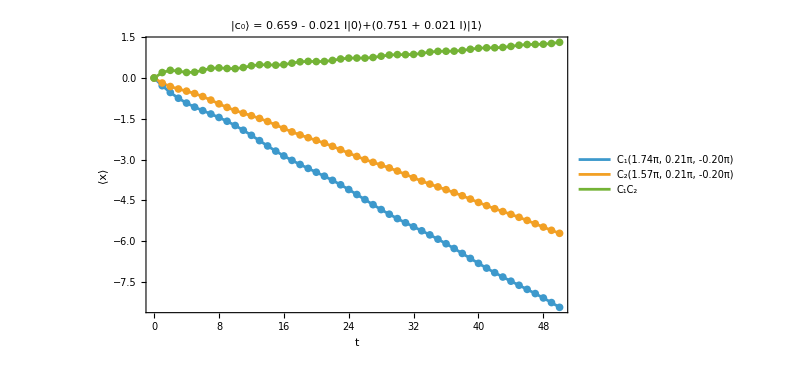
{-Graphics-,-Graphics3D-}

```mathematica
γ=1.1Pi/24.;
{θ1,α1,ϕ1}={1.74Pi,0.18Pi,1.74Pi+x};
{θ2,α2,ϕ2}={(1.57+0)Pi,(0.18+0)Pi,1.74Pi+x};
R=RotationMatrix[γ,Cross[nhat[α1,ϕ1],{1,0,0}]];
ψ0=Chop[MatrixExp[-I*(γ)/2*Normalize[Cross[nhat[α1,ϕ1],{1,0,0}]].(Pauli/@{1,2,3})]].Normalize[{1,1}];
{α1,ϕ1}={α2,ϕ2}={ArcCos[#3],ArcTan[#2/#1]}&@@(R.nhat[α1,ϕ1]);
u=c[θ1,α1,ϕ1].c[θ2,α2,ϕ2];
{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},tmax->50,FontSize->24],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0,u]}
```

```mathematica
Chop[MatrixExp[-I*Pi/2*Normalize[Cross[nhat[α1,ϕ1],{1,0,0}]].(Pauli/@{1,2,3})]].Normalize[{1,1}]
```

{0.64176+0.29689 ⅈ,-0.64176-0.29689 ⅈ}

```mathematica
R.{1,0,0}
```

{0.,0.419865,-0.907586}

```mathematica
{ArcCos[#3],ArcTan[#2/#1]}&@@(R.{1,0.3,0})
```

{2.48695,-1.38414}

```mathematica
nhat[α1,ϕ1].nhat[Pi/2.+y,0+z]
```

0.342026

```mathematica
u=c[1.74Pi,0.18Pi,1.74Pi].c[1.57Pi,(0.18-0.17)Pi,(1.74-0.1)Pi]
```

{{0.502714+0.836524 ⅈ,-0.0491417+0.212347 ⅈ},{0.0491417+0.212347 ⅈ,0.502714-0.836524 ⅈ}}

```mathematica
RotationAxisAndAngle[c[1.74Pi,Pi/2,6.5Pi/5].c[1.74Pi,Pi/2,8.5Pi/5]]/Pi
```

{0.416478,0.579283,-0.5}

```mathematica
1.31/Pi
```

0.416986

```mathematica
2Pi/5.
```

1.25664

```mathematica
RotationAxisAndAngle[c[1.74Pi,2.5Pi/10,6.5Pi/5].c[1.74Pi,7.5Pi/10,8.5Pi/5]]
```

{0.916777,1.74112,-1.86774}

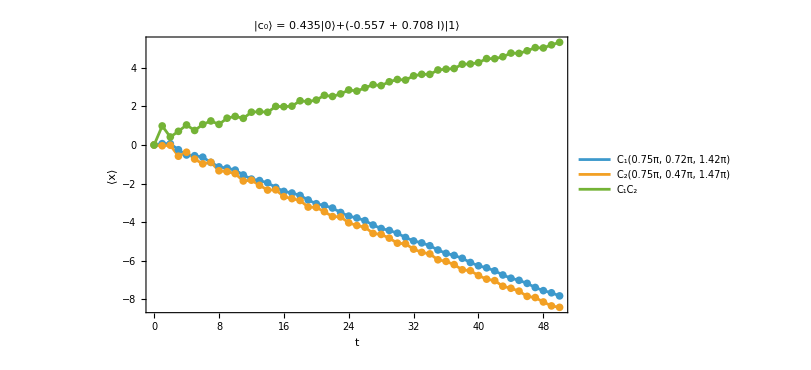
{-Graphics-,-Graphics3D-}

```mathematica
ψ0={0.435,-0.557+0.708I};
{θ1,α1,ϕ1}={0.75Pi,0.72Pi,1.42Pi};
{θ2,α2,ϕ2}={0.75Pi,(0.72-0.25)Pi,(1.42+0.05)Pi};
{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2}],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0]}
```

Rotar Pi el estado inicial

```mathematica
Pauli[3].{a,b}
```

{0.435+0. ⅈ,0.557-0.708 ⅈ}

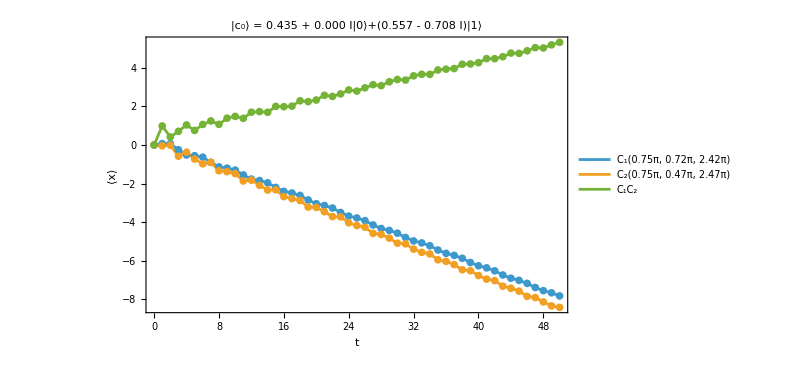
{-Graphics-,-Graphics3D-}

```mathematica
tmax=50;
ψ0=Pauli[3].{0.435,-0.557+0.708I};
{θ1,α1,ϕ1}={0.75Pi,0.72Pi,1.42Pi+Pi};
{θ2,α2,ϕ2}={0.75Pi,(0.72-0.25)Pi,(1.42+0.05)Pi+Pi};
{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2}],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0]}
```

```mathematica
SeedRandom[23802];
t=5;{a,b}=RandomQubitState[];
Manipulate[
Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[5]],{θ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[θ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π, ϕ = "<>ToString[NumberForm[ϕ/Pi,{Infinity,2}]]<>"π",Black,FontSize->28],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{α,0,Pi},{ϕ,0,2Pi}]
```

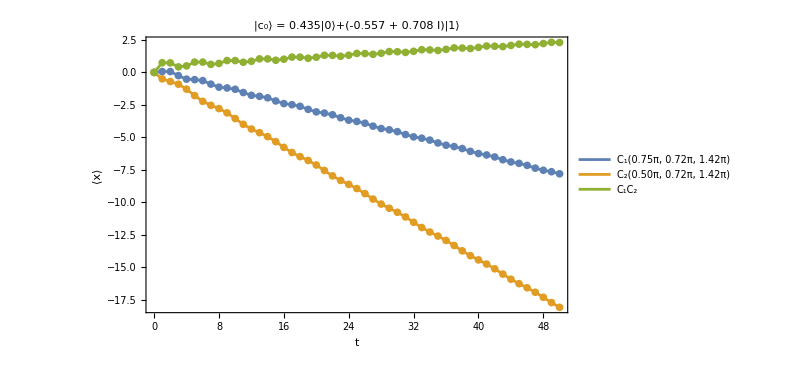

```mathematica
ψ0={a,b};tmax=50;
{θ1,α1,ϕ1}={3Pi/4.,0.72Pi,1.42Pi};
{θ2,α2,ϕ2}={2Pi/4.,0.72Pi,1.42Pi};
ListPlot[{Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1].c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}]},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm@HoldForm[t], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLegends->{"C_1("<>ToString[NumberForm[θ1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[α1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ1/Pi,{Infinity,2}]]<>"π)","C_2("<>ToString[NumberForm[N[θ2/Pi],{Infinity,2}]]<>"π, "<>ToString[NumberForm[α2/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ2/Pi,{Infinity,2}]]<>"π)","C_1C_2"},
PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+("<>ToString[NumberForm[b,{Infinity,3}]]<>")|1⟩",Black,FontSize->28],
LabelStyle->Directive[Black,FontSize->28]
]
```

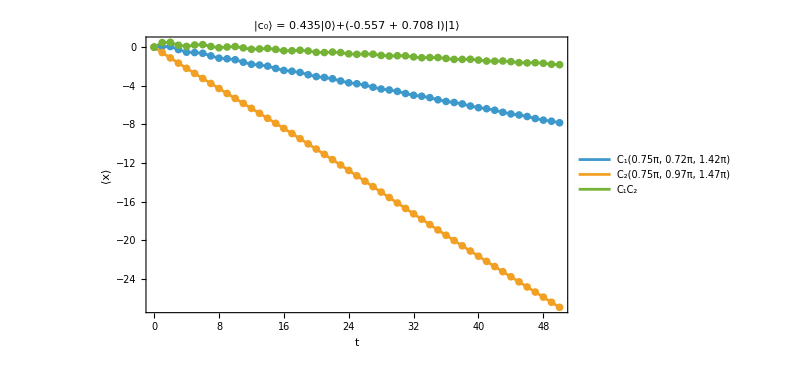
{-Graphics-,-Graphics3D-}

```mathematica
tmax=50;
ψ0={a,b}={0.435,-0.557+0.708I};
{θ1,α1,ϕ1}={0.75Pi,0.72Pi,1.42Pi};
{θ2,α2,ϕ2}={0.75Pi,(0.72+0.25)Pi,(1.42+0.05)Pi};
{ListPlot[{Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1].c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}]},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm@HoldForm[t], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLegends->{"C_1("<>ToString[NumberForm[θ1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[α1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ1/Pi,{Infinity,2}]]<>"π)","C_2("<>ToString[NumberForm[N[θ2/Pi],{Infinity,2}]]<>"π, "<>ToString[NumberForm[α2/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ2/Pi,{Infinity,2}]]<>"π)","C_1C_2"},
PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+("<>ToString[NumberForm[b,{Infinity,3}]]<>")|1⟩",Black,FontSize->28],
LabelStyle->Directive[Black,FontSize->28]
],
PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0]
}
```

## Todo de una forma más sistemática

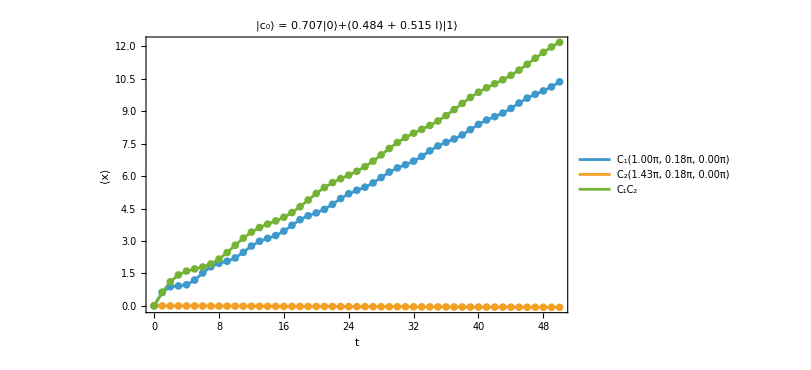
{-Graphics-,-Graphics3D-}

```mathematica
(*Estado inicial*)
{θ,ϕ}={0.5,-1.74}Pi;
ψ0=Chop@{Cos[θ/2],Exp[I ϕ]Sin[θ/2]};

(*Parametros monedas*)
α1=α2=0.18Pi(*polar*);
{θ1,θ2}={1.,1.43}Pi(*angulo de rotacion*);
ϕ1=ϕ2=0.(*azimuthal*);
u=c[θ1,α1,ϕ1].c[θ2,α2,ϕ2](*C1.C2*);

{PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},tmax->50,FontSize->20],PlotSphere[{α1,ϕ1},{α2,ϕ2},ψ0,u]}
```

```mathematica
{tmin,tmax,dt}={25,75,25};

Manipulate[
ListPlot[Table[{#,Chop@ExpValPosition[DTQW[{Cos[θ Pi/2],Exp[I ϕ Pi]Sin[θ Pi/2]},t,c[#,0.25*Pi,0.]],t]}&/@Range[0,2Pi,0.025Pi],{t,tmin,tmax,dt}],
PlotRange->{Automatic,{-r,r}},
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
Frame->True,
FrameLabel->{"θ", },
FrameStyle->Directive[Black,FontSize->22],
ImageSize->650,
PlotLabel->Style["C=H, |c_0(θ="<>ToString[NumberForm[θ,{Infinity,3}]]<>"π, ϕ="<>ToString[NumberForm[ϕ,{Infinity,3}]]<>"π)⟩ = "<>ToString[NumberForm[Cos[θ Pi/2],{Infinity,3}]]<>"|0⟩ + "<>ToString[NumberForm[Exp[I ϕ Pi]Sin[θ Pi/2],{Infinity,3}]]<>"|1⟩",Black,FontSize->22],
PlotLegends->Range[tmin,tmax,dt],
LabelStyle->Directive[Black,FontSize->22],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{θ,0,1,0.05},{ϕ,0,2,0.1},{r,70,10,-10}]
```

Anti-Parrondo

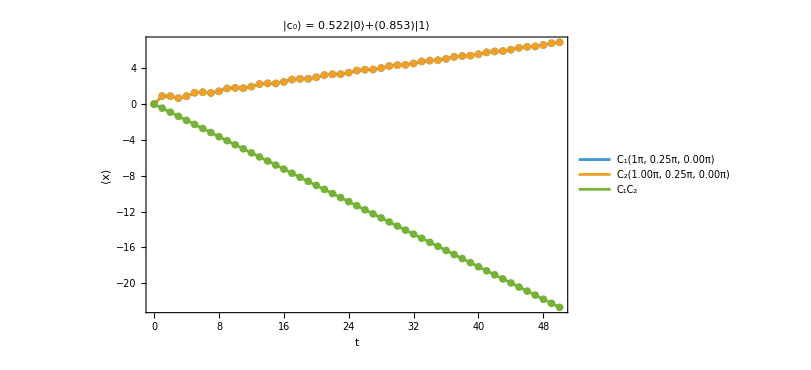

```mathematica
{θ,ϕ}={0.65,0.}Pi;
ψ0=Chop@{Cos[θ/2],Exp[I ϕ]Sin[θ/2]};

{θ1,α1,ϕ1}={θ2,α2,ϕ2}={Pi,Pi/4.,0.};
PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},MaxTime->50,FontSize->20,PlotLegendsPosition->{Left,Bottom}]
```

Parrondo

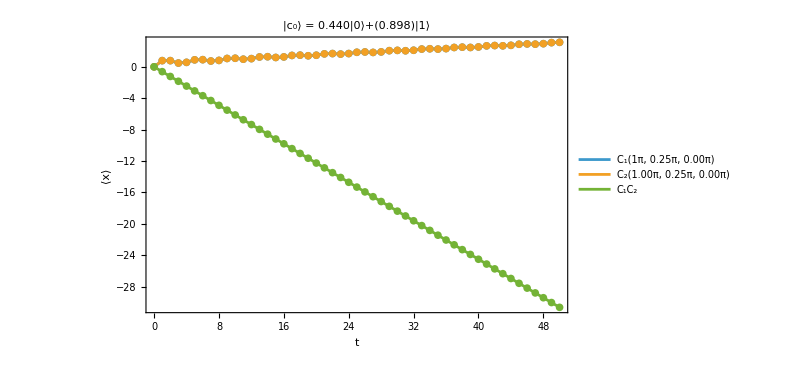

```mathematica
{θ,ϕ}={0.71,0.}Pi;
ψ0=Chop@{Cos[θ/2],Exp[I ϕ]Sin[θ/2]};

{θ1,α1,ϕ1}={θ2,α2,ϕ2}={Pi,Pi/4.,0.};
PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},MaxTime->50,FontSize->20,PlotLegendsPosition->{Left,Bottom}]
```

```mathematica
{tmin,tmax,dt}={25,75,25};

Manipulate[
ListPlot[Table[{#,ExpValPosition[DTQW[Chop[{Cos[#/2],Exp[I ϕ Pi]Sin[#/2]}],t,Exp[I Pi/2]c[Pi,0.25*Pi,0]],t]}&/@Range[0,2Pi,0.05Pi],{t,tmin,tmax,dt}],
PlotRange->{Automatic,{-r,r}},
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
Frame->True,
FrameLabel->{"θ", },
FrameStyle->Directive[Black,FontSize->22],
ImageSize->650,
(*PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[ψ0[[1]],{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[ψ0[[2]],{Infinity,3}]]<>"|1⟩, ϕ = "<>ToString[NumberForm[0./Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->22],*)
PlotLegends->Range[tmin,tmax,dt],
LabelStyle->Directive[Black,FontSize->22],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{ϕ,0,2,0.1},{r,10,70,10}]
```

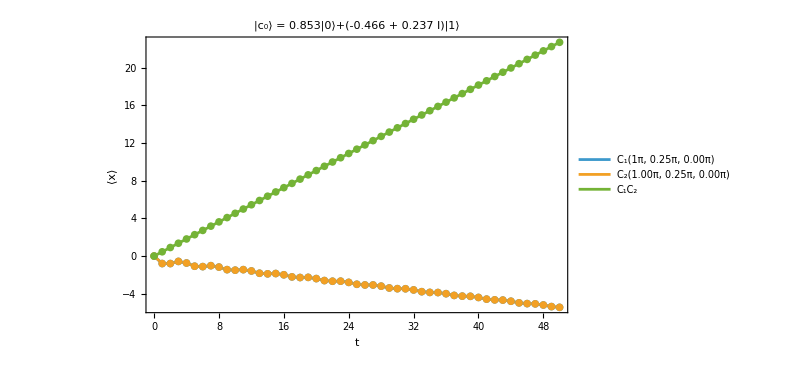

```mathematica
{θ,ϕ}={0.35,0.85}Pi;
ψ0=Chop@{Cos[θ/2],Exp[I ϕ]Sin[θ/2]};

{θ1,α1,ϕ1}={θ2,α2,ϕ2}={Pi,Pi/4.,0.};
PlotExpValPosition[ψ0,{θ1,α1,ϕ1},{θ2,α2,ϕ2},MaxTime->50,FontSize->20]
```

```mathematica
Chop[Exp[I Pi/2]c[Pi,0.25*Pi,0]]
```

{{0.707107,0.707107},{0.707107,-0.707107}}

```mathematica
Chop[Exp[I*Pi/2]c[Pi,Pi/4.,0.]]
```

{{0.707107,0.707107},{0.707107,-0.707107}}

```mathematica
Chop[c[Pi,Pi/4,Pi/4]]//MatrixForm
```

(0.-0.707107 ⅈ | -0.5-0.5 ⅈ
0.5-0.5 ⅈ | 0.+0.707107 ⅈ)

```mathematica
HadamardMatrix[2]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
{θ,ϕ}={0.5,0.}Pi;α=0.35Pi;
ψ0=Chop@{Cos[θ/2],Exp[I ϕ]Sin[θ/2]};
PlotSphere[{α,0.},{α,0.},ψ0,-c[0.5Pi,α,0].c[0.5Pi,α,0]]
```

-Graphics3D-

## Haddamard walk (No parrondo)

```mathematica
{tmin,tmax,dt}={25,75,25};

Manipulate[
ψ0=Chop[{Cos[θ Pi/2],Exp[I ϕ Pi]Sin[θ Pi/2]}];

ListPlot[Table[{#,ExpValPosition[DTQW[ψ0,t,H],t]}&/@Range[0,2Pi,0.025Pi],{t,tmin,tmax,dt}],
PlotRange->{Automatic,{-r,r}},
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
Frame->True,
FrameLabel->{"θ", },
FrameStyle->Directive[Black,FontSize->22],
ImageSize->650,
PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[ψ0[[1]],{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[ψ0[[2]],{Infinity,3}]]<>"|1⟩",Black,FontSize->22],
PlotLegends->Range[tmin,tmax,dt],
LabelStyle->Directive[Black,FontSize->22],
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}}
]
,{θ,0,1,0.05},{ϕ,0,2,0.1},{r,10,70,10}]
```

```mathematica
{θ,ϕ}={0.6,0.}Pi;
ψ0=Chop@{Cos[θ/2],Exp[I ϕ]Sin[θ/2]};
PlotSphere[{Pi/4.,0.},{Pi/4.,0.},ψ0,-c[Pi,Pi/4,0]]
```

-Graphics3D-

## Variando otras cosas no

```mathematica
t=5;
SeedRandom[23802];
t=5;{a,b}=RandomQubitState[];
Manipulate[Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[4,5]],{ϕ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[ϕ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+("<>ToString[NumberForm[b,{Infinity,3}]]<>")|1⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28]
],{α,0,Pi},{θ,0,2Pi}]
```

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::prng: Value of option PlotRange -> {All,{-1.05 t,1.05 t}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[$Failed,2.].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

```mathematica
t=5;
SeedRandom[23505];
t=5;{a,b}=RandomQubitState[];
Manipulate[Plot[Evaluate[ExpPosition[DTQWAnalytical[ArrayPad[{a,b},2],#,θ,α,ϕ]]&/@Range[5]],{ϕ,0,2Pi},
PlotRange->{All,{-(t+0.05t),t+0.05t}},
Frame->True,
FrameLabel->{HoldForm[ϕ], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->800,
FrameTicks->{{Automatic,Automatic},{Table[{k Pi/4,ToString[TraditionalForm[k Pi/4]]},{k,0,8}],Automatic}},
PlotLabel->Style["t = "<>ToString[t]<>", |c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+("<>ToString[NumberForm[b,{Infinity,3}]]<>")|1⟩, θ = "<>ToString[NumberForm[θ/Pi,{Infinity,2}]]<>"π, α = "<>ToString[NumberForm[α/Pi,{Infinity,2}]]<>"π",Black,FontSize->28]
],{α,0,Pi},{θ,0,2Pi}]
```

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

Partition::pdep: Depth 1 requested in object with dimensions {}.

DTQWAnalytical::invalidpsi0: ψ0 debe ser una lista de 6 elementos numéricos. Se recibió: {0,0,a,b,0,0}.

General::stop: Further output of DTQWAnalytical::invalidpsi0 will be suppressed during this calculation.

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {All,{-1.05 t,1.05 t}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[$Failed,2.].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

```mathematica
α=Pi/4.;θ=0.66Pi;ϕ=Pi/2.+Pi;
```

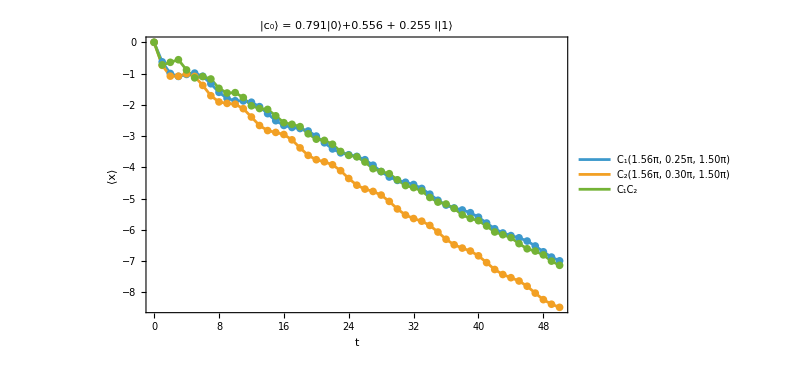

```mathematica
ψ0={a,b};tmax=50;
{θ1,α1,ϕ1}={1.56Pi,Pi/4.,3Pi/2.};
{θ2,α2,ϕ2}={1.56Pi,Pi/4+0.05Pi,3Pi/2.};
ListPlot[{Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}],Prepend[Table[{t,ExpValPosition[DTQW[ψ0,t,c[θ1,α1,ϕ1].c[θ2,α2,ϕ2]],t]},{t,tmax}],{0,0}]},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{TraditionalForm@HoldForm[t], "⟨x⟩"},
FrameStyle->Directive[Black,FontSize->28],
ImageSize->600,
PlotLegends->{"C_1("<>ToString[NumberForm[θ1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[α1/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ1/Pi,{Infinity,2}]]<>"π)","C_2("<>ToString[NumberForm[N[θ2/Pi],{Infinity,2}]]<>"π, "<>ToString[NumberForm[α2/Pi,{Infinity,2}]]<>"π, "<>ToString[NumberForm[ϕ2/Pi,{Infinity,2}]]<>"π)","C_1C_2"},
PlotLabel->Style["|c_0⟩ = "<>ToString[NumberForm[a,{Infinity,3}]]<>"|0⟩+"<>ToString[NumberForm[b,{Infinity,3}]]<>"|1⟩",Black,FontSize->28],
LabelStyle->Directive[Black,FontSize->28]
]
```